```mathematica
gl=Import["C:\\cloud\\github\\a-boy\\playmath\\stage17-Ramsey-Numbers\\r36_17.g6"];
VertexDegree/@gl
IsomorphicGraphQ[gl[[6]],gl[[7]]]
```

{{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}}

False

{1<->2,1<->3,1<->4,1<->5,2<->6,2<->7,2<->14,2<->15,3<->12,3<->13,3<->15,3<->17,4<->10,4<->11,4<->16,4<->17,5<->8,5<->9,5<->14,5<->16,6<->8,6<->10,6<->12,6<->17,7<->9,7<->11,7<->13,7<->17,8<->11,8<->13,8<->15,9<->10,9<->12,9<->15,10<->13,10<->14,11<->12,11<->14,12<->16,13<->16,14<->17,15<->16}

{1<->2,1<->3,1<->4,1<->5,2<->6,2<->7,2<->14,2<->15,3<->11,3<->12,3<->15,3<->17,4<->8,4<->10,4<->16,4<->17,5<->9,5<->13,5<->14,5<->16,6<->9,6<->12,6<->13,6<->17,7<->10,7<->11,7<->13,7<->17,8<->11,8<->12,8<->13,8<->14,9<->10,9<->11,9<->15,10<->12,10<->14,11<->16,12<->16,13<->15,14<->17,15<->16}

<|1→1,2→2,7→3,13→4,5→5,14→6,10→7,9→8,11→9,8→10,12→11,6→12,17→13,4→14,16→15,15→16,3→17|>

{1<->2,1<->17,1<->14,1<->5,2<->3,2<->12,2<->9,2<->16,17<->7,17<->11,17<->16,17<->13,14<->10,14<->8,14<->15,14<->13,5<->4,5<->6,5<->9,5<->15,3<->4,3<->10,3<->7,3<->13,12<->6,12<->8,12<->11,12<->13,4<->8,4<->11,4<->16,6<->10,6<->7,6<->16,10<->11,10<->9,8<->7,8<->9,7<->15,11<->15,9<->13,16<->15}

{1<->2,1<->17,1<->14,1<->5,2<->12,2<->3,2<->6,2<->16,17<->9,17<->11,17<->16,17<->13,14<->10,14<->7,14<->15,14<->13,5<->8,5<->4,5<->6,5<->15,12<->8,12<->11,12<->4,12<->13,3<->7,3<->9,3<->4,3<->13,10<->9,10<->11,10<->4,10<->6,8<->7,8<->9,8<->16,7<->11,7<->6,9<->15,11<->15,4<->16,6<->13,16<->15}

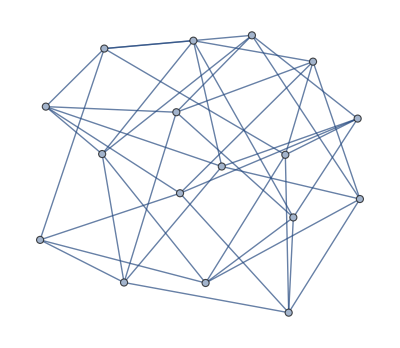
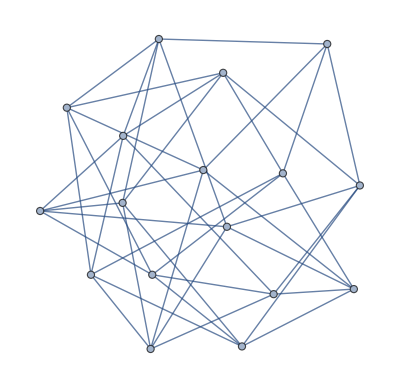

```mathematica
EdgeList[gl[[6]]]
EdgeList[gl[[7]]]
assoc6=<|1->1,2->2,6->3,8->4,5->5,9->6,12->7,11->8,14->9,10->10,13->11,7->12,17->13,4->14,16->15,15->16,3->17|>;
assoc7=<|1->1,2->2,7->3,13->4,5->5,14->6,10->7,9->8,11->9,8->10,12->11,6->12,17->13,4->14,16->15,15->16,3->17|>
e6=EdgeList[gl[[6]]]/.assoc6
e7=EdgeList[gl[[7]]]/.assoc7
{Graph[e6],Graph[e7]}
```